## VE401 RC 2

## Continuous Random Variables

#### Exponential Distribution

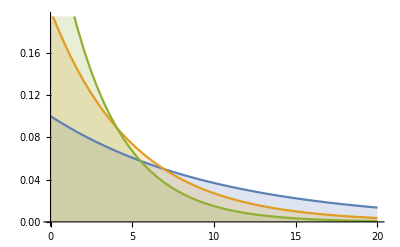

```mathematica
Plot[Table[PDF[ExponentialDistribution[β], x], {β, {0.1, 0.2, 0.3}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Gamma Distribution

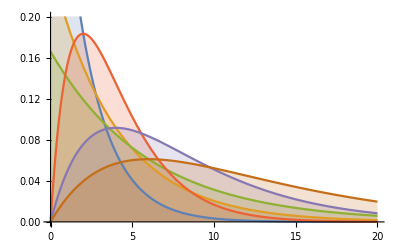

```mathematica
Plot[Table[PDF[GammaDistribution[α, β], x], {α, {1, 2}}, {β, {2, 4, 6}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Chi-Squared Distribution

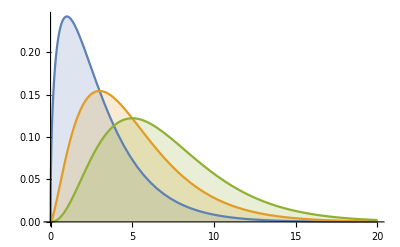

```mathematica
Plot[Table[PDF[ChiSquareDistribution[γ], x], {γ, {3, 5, 7}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Normal Distribution

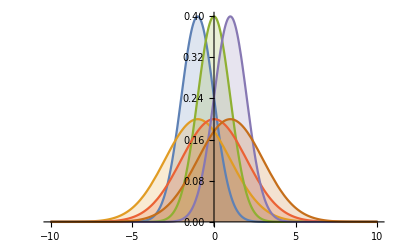

```mathematica
Plot[Table[PDF[NormalDistribution[μ, σ], x], {μ, {-1, 0, 1}}, {σ, {1, 2}}] // Evaluate, {x, -10, 10}, Filling->Axis]
```

## VE401 RC 4

## Statistical Distributions

### Standard Normal Distribution

```mathematica
InverseCDF[NormalDistribution[0, 1], 0.95]
```

1.64485

```mathematica
InverseCDF[NormalDistribution[0, 1], 0.975]
```

1.95996

### Chi-squared Distribution

```mathematica
InverseCDF[ChiSquareDistribution[10], 0.95]
```

18.307

### T Distribution

```mathematica
InverseCDF[StudentTDistribution[10], 0.95]
```

1.81246

## Case Study

```mathematica
X = Round[RandomVariate[NormalDistribution[4.5, 2], 70], 0.01]
```

{1.67,3.6,2.67,11.3,3.86,2.67,4.43,5.86,3.12,2.86,7.24,3.31,4.98,6.68,3.27,6.32,3.94,4.14,4.9,1.98,7.27,5.84,1.33,7.86,4.12,2.39,9.,5.03,6.03,7.85,1.94,3.52,5.49,6.57,8.9,7.73,5.18,4.3,7.37,5.02,6.82,1.24,3.66,0.94,2.22,5.37,3.13,2.44,3.43,3.89,4.53,1.37,4.88,3.15,1.63,0.62,3.49,3.06,2.76,5.47,3.26,5.77,6.64,5.74,2.19,1.42,3.82,2.76,2.29,6.93}

```mathematica
{q1, q2, q3} = Quartiles[X]
iqr = InterquartileRange[X]
h = 2iqr / Sqrt[70]
Min[X]-0.005
n=70
```

{2.76,3.915,5.84}

3.08

0.736261

0.615

70

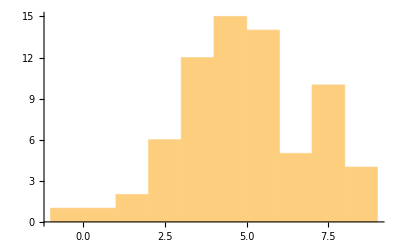

```mathematica
Histogram[X, "FreedmanDiaconis"]
```

```mathematica
Needs["StatisticalPlots`"]
StemLeafPlot[Floor[X, 0.1], IncludeEmptyStems->True]
```

Stem | Leaves
0 | 69
1 | 23346699
2 | 1223466778
3 | 0111223445668889
4 | 11345899
5 | 0013447788
6 | 0356689
7 | 223788
8 | 9
9 | 0
10 | 
11 | 3
Stem units: 1

```mathematica
f1 = q1 - 3/2*iqr
f3 = q3 + 3/2 *iqr
F1 = q1 - 3iqr
F3 = q3 + 3iqr
a1 = Min[Select[X, #≥f1&]]
a3 = Max[Select[X, #≤f3&]]
```

-1.86

10.46

-6.48

15.08

0.62

9.

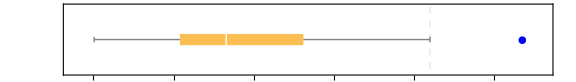

```mathematica
BoxWhiskerChart[
X, {"Outliers", {"Outliers",Blue},{"FarOutliers",Red}},
AspectRatio->1/7, BarOrigin->Left,
GridLines->{{{a3,Dashed},{F3,Dashed}},None},ImageSize->Large,FrameTicks->{
{None,None},
{Range[Min[Floor[X,0.1]],Max[Ceiling[X,0.1]]],
{{q1,"q1"},{q2,"q2"},{q3,"q3"},{a3,"near"},{F3,"far"}}}}
]
```

```mathematica
Mean[X]
Variance[X]
```

4.378

4.89576

```mathematica
z = InverseCDF[NormalDistribution[0, 1], 0.975]
Mean[X]-2z/Sqrt[70]
Mean[X]+2z/Sqrt[70]
```

1.95996

3.90948

4.84652

```mathematica
c1 = InverseCDF[ChiSquareDistribution[69], 0.025]
c2 = InverseCDF[ChiSquareDistribution[69], 0.975]
(n-1)Variance[X]/c2
(n-1)Variance[X]/c1
```

47.9242

93.8565

3.59919

7.04879

```mathematica
t = InverseCDF[StudentTDistribution[69], 0.975]
Mean[X] - t Variance[X]/Sqrt[n]
Mean[X] + t Variance[X]/Sqrt[n]
```

1.99495

3.21065

5.54535